```mathematica
generateNe[seed_,size_]:=Module[{n=Length@IntegerDigits@seed,x=seed,squarex, digits, value},
Return[Table[squarex=x^2;digits=IntegerDigits[squarex,10,2n];value=FromDigits[digits[[n/2+1;;n/2+n]]];x=value;
N@FromDigits[{{value},1-n}],{i,size}]]]
```

{0.230946,0.6143,0.434748,0.603331,0.871101,0.77963,0.264111,0.453649,0.761417,0.607616,0.742694,0.396143,0.930497,0.490838,0.193616,0.706283,0.569897,0.288342,0.123261,0.31532,0.684108,0.345247,0.531031,0.358183,0.483139,0.351972,0.428808,0.630567,0.431888,0.751301,0.254303,0.982976,0.202477,0.694881,12256,0.127351,0.838285,0.200294,0.759033,0.185352,0.51794,0.234766,0.504865,0.867055,0.391851,0.758528,0.440684,0.211763,0.351163,0.533289,0.744315,0.491747,0.556284,0.220674,0.698215,0.36095,0.487218,0.139911,0.509251,0.658925,0.226975,0.768771,0.926881,0.769337,0.959529,0.505419,0.869671,0.79328,0.274225}
 |  |  |  |

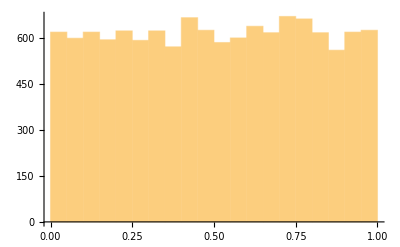

```mathematica
result=generateNe[1134121222,12324]
Histogram[result]
```